```mathematica
(* Misc plots for disseration *)
```

```mathematica
(* Landau levels *)
```

3/2

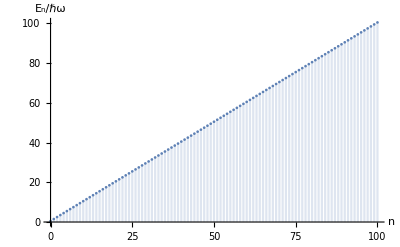

```mathematica
hbar=1;
ω=1;
ϵ[n_Integer]:=hbar*ω*(n+1/2);
ϵ[1]
DiscretePlot[ϵ[n],{n,0,100},TicksStyle->Directive[Black, FontSize->48],AxesLabel->{"n","E_n/ℏω"},LabelStyle->Directive[Black,FontSize->48]]
```

```mathematica
Show[%57,ImageSize->Full]
```

-Graphics-

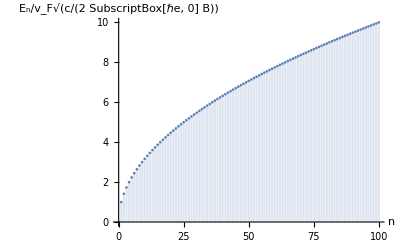

```mathematica
η[n_Integer]:=√n;
DiscretePlot[η[n],{n,0,100},TicksStyle->Directive[Black, FontSize->48],AxesLabel->{"n","E_n/v_F√(c/(2 SubscriptBox[ℏe, 0] B))"},LabelStyle->Directive[Black,FontSize->48]]
```

```mathematica
Show[%69,ImageSize->Full]
```

-Graphics-